```mathematica
pic = Import["C:\\Users\\tatki\\Downloads\\PVR016_000.bmp"]
```

-Graphics-

```mathematica
pic1=ColorConvert[pic, "Grayscale"]
```

-Graphics-

```mathematica
pic2=ImageAdjust[ImageCrop[pic1, {200,200}]]
```

-Graphics-

```mathematica
table=ImageData[pic2]
```

{1}
 |  |  |  |

```mathematica
data=Dataset[table]
```

Dataset[<>]

```mathematica
row=data[100]
```

Dataset[<>]

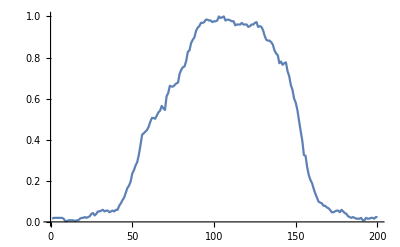

```mathematica
ListLinePlot[row]
```

```mathematica
ListPlot3D[data,PlotTheme->"Classic",ImageSize->Large]
```

```mathematica
-Graphics3D-
Rotate[ListPlot3D[data],180 Degree,{1,0,0}]
```

```mathematica
model[x_]=ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]];
fit=Normal[FindFit[row,model[x],{ampl,x0,sigma},x]]
```

{ampl→88.5312,x0→108.016,sigma→33.1797}

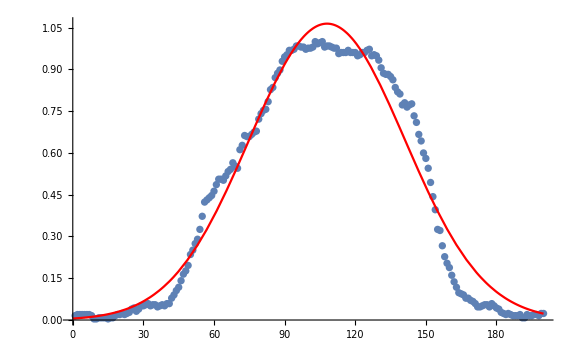

```mathematica
Show[ListPlot[row],Plot[model[x]/.fit,{x,0,200},PlotStyle->Red],ImageSize->Large,PlotRange->All]
```